# ZA ZAČETEK

# OSNOVNA ARITMETIKA

V seznam lahko vržemo, kar hočemo

```mathematica
seznam={1,(Sin@Log@x)/(a+a/(a+a/(a+a/(a-Graphics-)))),({{-Graphics-, 1, -Graphics-}, {3, 8, 6}, {4, 1, 6}})}
```

{1,Sin[Log[x]]/(a+a/(a+a/(a+-Graphics-))),{{-Graphics-,1,-Graphics-},{3,8,6},{4,1,6}}}

Tako se s seznami računa:

```mathematica
{1,2,3,4,{5,6},7,{8,9,{{{10}},11,12}},13,14}  +  1
```

{2,3,4,5,{6,7},8,{9,10,{{{11}},12,13}},14,15}

```mathematica
{1,2,3,4,{5,6},7,{8,9,{{{10}},11,12}},13,14}  *  2
```

{2,4,6,8,{10,12},14,{16,18,{{{20}},22,24}},26,28}

```mathematica
{{1,2,3},{4,5,6,7}}  +  {{a,b,c},{č,d,e,f}}
```

{{1+a,2+b,3+c},{4+č,5+d,6+e,7+f}}

```mathematica
{{1,2,3},{4,5,6,{7,8}}}  +  {1,2}
```

{{2,3,4},{6,7,8,{9,10}}}

```mathematica
a=({{{1,2}, {3,4}, {5,6}}, {{7,8}, {9,10}, {11,12}}, {{13,14}, {15,16}, {17,18}}});
a+Threaded[{1,2},3]
```

{{{2,4},{4,6},{6,8}},{{8,10},{10,12},{12,14}},{{14,16},{16,18},{18,20}}}

# ROČNO UREJANJE

Ctrl+Enter    in      Ctrl+,

probejte iz zgornje dobit srednjo in pol vanjo iz spodnje skopirat kak blok (z miško in pol še Shift+Puščcami)

```mathematica
()
({{□, □, □, □, □}, {□, □, □, □, □}, {□, □, □, □, □}})
({{1, 2, 3, 4, 5}, {6, 7, 8, 9, 0}, {1, 2, 3, 4, 5}})
```

Arraysi so seznami oblike d_1×...×d_2 (hiperkvadrasti)

Packed arraysi se računajo veliko hitreje, kot vse ostalo. To so arraysi, napolnjeni s števili iste vrste.

# Range, Subdivide, Array

```mathematica
Remove["Global`*"];
Range[1,100,15]
Range[100,-10,-15]
Subdivide[0,10,11]
Subdivide[10,0,11]
MatrixForm/@{
	Array[#1+3#2&,{4,3}],
	Array[f[#1,#2]&,{4,3}]
}
```

{1,16,31,46,61,76,91}

{100,85,70,55,40,25,10,-5}

{0,10/11,20/11,30/11,40/11,50/11,60/11,70/11,80/11,90/11,100/11,10}

{10,100/11,90/11,80/11,70/11,60/11,50/11,40/11,30/11,20/11,10/11,0}

{(4 | 7 | 10
5 | 8 | 11
6 | 9 | 12
7 | 10 | 13),(f[1,1] | f[1,2] | f[1,3]
f[2,1] | f[2,2] | f[2,3]
f[3,1] | f[3,2] | f[3,3]
f[4,1] | f[4,2] | f[4,3])}

## PRIKAZ, Table, ParallelTable

```mathematica
Table[
	RandomInteger[{0,9}],
5,10,3]
```

{{{7,7,6},{7,7,1},{8,3,7},{4,1,2},{9,7,6},{1,7,1},{7,5,2},{1,1,8},{1,3,3},{2,8,3}},{{6,9,6},{1,8,1},{1,3,6},{5,7,0},{4,5,8},{5,1,6},{4,6,6},{5,8,1},{8,7,5},{9,3,3}},{{9,1,1},{2,5,9},{3,4,7},{3,0,0},{5,5,8},{3,5,6},{8,5,3},{7,8,0},{8,7,6},{3,1,9}},{{2,2,7},{3,9,3},{0,2,3},{2,0,9},{0,2,2},{6,3,4},{7,9,9},{2,9,2},{1,7,2},{3,8,4}},{{2,3,5},{6,3,4},{6,5,5},{2,8,4},{1,2,6},{1,8,4},{9,0,3},{3,5,2},{3,0,4},{6,9,9}}}

```mathematica
MatrixForm@%
```

((7
7
6) | (7
7
1) | (8
3
7) | (4
1
2) | (9
7
6) | (1
7
1) | (7
5
2) | (1
1
8) | (1
3
3) | (2
8
3)
(6
9
6) | (1
8
1) | (1
3
6) | (5
7
0) | (4
5
8) | (5
1
6) | (4
6
6) | (5
8
1) | (8
7
5) | (9
3
3)
(9
1
1) | (2
5
9) | (3
4
7) | (3
0
0) | (5
5
8) | (3
5
6) | (8
5
3) | (7
8
0) | (8
7
6) | (3
1
9)
(2
2
7) | (3
9
3) | (0
2
3) | (2
0
9) | (0
2
2) | (6
3
4) | (7
9
9) | (2
9
2) | (1
7
2) | (3
8
4)
(2
3
5) | (6
3
4) | (6
5
5) | (2
8
4) | (1
2
6) | (1
8
4) | (9
0
3) | (3
5
2) | (3
0
4) | (6
9
9))

```mathematica
Normal@%
```

{{{7,7,6},{7,7,1},{8,3,7},{4,1,2},{9,7,6},{1,7,1},{7,5,2},{1,1,8},{1,3,3},{2,8,3}},{{6,9,6},{1,8,1},{1,3,6},{5,7,0},{4,5,8},{5,1,6},{4,6,6},{5,8,1},{8,7,5},{9,3,3}},{{9,1,1},{2,5,9},{3,4,7},{3,0,0},{5,5,8},{3,5,6},{8,5,3},{7,8,0},{8,7,6},{3,1,9}},{{2,2,7},{3,9,3},{0,2,3},{2,0,9},{0,2,2},{6,3,4},{7,9,9},{2,9,2},{1,7,2},{3,8,4}},{{2,3,5},{6,3,4},{6,5,5},{2,8,4},{1,2,6},{1,8,4},{9,0,3},{3,5,2},{3,0,4},{6,9,9}}}

```mathematica
TableForm@%
```

7
7
6 | 7
7
1 | 8
3
7 | 4
1
2 | 9
7
6 | 1
7
1 | 7
5
2 | 1
1
8 | 1
3
3 | 2
8
3
6
9
6 | 1
8
1 | 1
3
6 | 5
7
0 | 4
5
8 | 5
1
6 | 4
6
6 | 5
8
1 | 8
7
5 | 9
3
3
9
1
1 | 2
5
9 | 3
4
7 | 3
0
0 | 5
5
8 | 3
5
6 | 8
5
3 | 7
8
0 | 8
7
6 | 3
1
9
2
2
7 | 3
9
3 | 0
2
3 | 2
0
9 | 0
2
2 | 6
3
4 | 7
9
9 | 2
9
2 | 1
7
2 | 3
8
4
2
3
5 | 6
3
4 | 6
5
5 | 2
8
4 | 1
2
6 | 1
8
4 | 9
0
3 | 3
5
2 | 3
0
4 | 6
9
9

```mathematica
Grid[Normal@%, Frame->All]
```

```mathematica
{{{7,7,6}, {7,7,1}, {8,3,7}, {4,1,2}, {9,7,6}, {1,7,1}, {7,5,2}, {1,1,8}, {1,3,3}, {2,8,3}}, {{6,9,6}, {1,8,1}, {1,3,6}, {5,7,0}, {4,5,8}, {5,1,6}, {4,6,6}, {5,8,1}, {8,7,5}, {9,3,3}}, {{9,1,1}, {2,5,9}, {3,4,7}, {3,0,0}, {5,5,8}, {3,5,6}, {8,5,3}, {7,8,0}, {8,7,6}, {3,1,9}}, {{2,2,7}, {3,9,3}, {0,2,3}, {2,0,9}, {0,2,2}, {6,3,4}, {7,9,9}, {2,9,2}, {1,7,2}, {3,8,4}}, {{2,3,5}, {6,3,4}, {6,5,5}, {2,8,4}, {1,2,6}, {1,8,4}, {9,0,3}, {3,5,2}, {3,0,4}, {6,9,9}}}
```

```mathematica
Remove["Global`*"];
{dim1,dim2}={30,20};

Map[AbsoluteTiming@ReleaseHold@#&,Hold/@Unevaluated[{



	Table[
		NIntegrate[Sin[(Log[x+2]+x^6.51)/(ArcSinh@x)],{x,0,1}],
	dim1,dim2],
	
	
	ParallelTable[
		NIntegrate[Sin[(Log[x+2]+x^6.51)/(ArcSinh@x)],{x,0,1}],
	dim1,dim2],
	
	
	intg=NIntegrate[Sin[(Log[x+2]+x^6.51)/(ArcSinh@x)],{x,0,1}],
	
	
	Table[intg,dim1,dim2],
	
	ConstantArray[intg,{dim1,dim2}]
	
	

}]][[;;,1]]
```

{6.3283,1.01644,0.0147348,0.0000564,1.7×10^-6}

```mathematica
l0=1.0;  ω=100.0;  c1=.2;  g=9.81;
φ0=70°;  v0l=1.0;
T=60.0; dt=.00001;


r=l0{Sin@φ0,0,-Cos@φ0};
v={0,v0l,0};

rjivji=Table[
	{r,v}+={v,{0,0,-g} - ω^2 (Norm@r-l0) Normalize@r - c1 v}dt;
	{r,v},
{t,0,T,dt}];
```

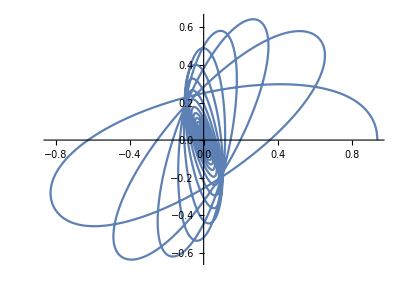

```mathematica
Ntočk=1000;
ListLinePlot[
	rjivji[[1;;-1;;Round[(T/dt)/Ntočk],  1,  ;;2]],
	AspectRatio->Automatic,PlotRange->All, InterpolationOrder->2
]
```

```mathematica
Remove[r,v];

l0=1.0;  ω=100.0;  c1=.2;  g=9.81;
φ0=70°;  v0l=1.0;
T=60.0; dt=.00001;


r=l0{Sin@φ0,0,-Cos@φ0};
v={0,v0l,0};

rjivjiP=ParallelTable[
	{r,v}+={v,{0,0,-g} - ω^2 (Norm@r-l0) Normalize@r - c1 v}dt;
	{r,v},
{t,0,T,dt}];
```

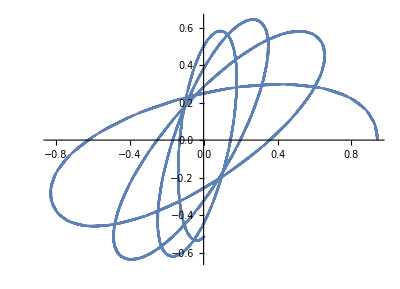

```mathematica
Ntočk=1000;
ListLinePlot[
	rjivjiP[[1;;-1;;Round[(T/dt)/Ntočk],  1,  ;;2]],
	AspectRatio->Automatic,PlotRange->All, InterpolationOrder->2
]
```

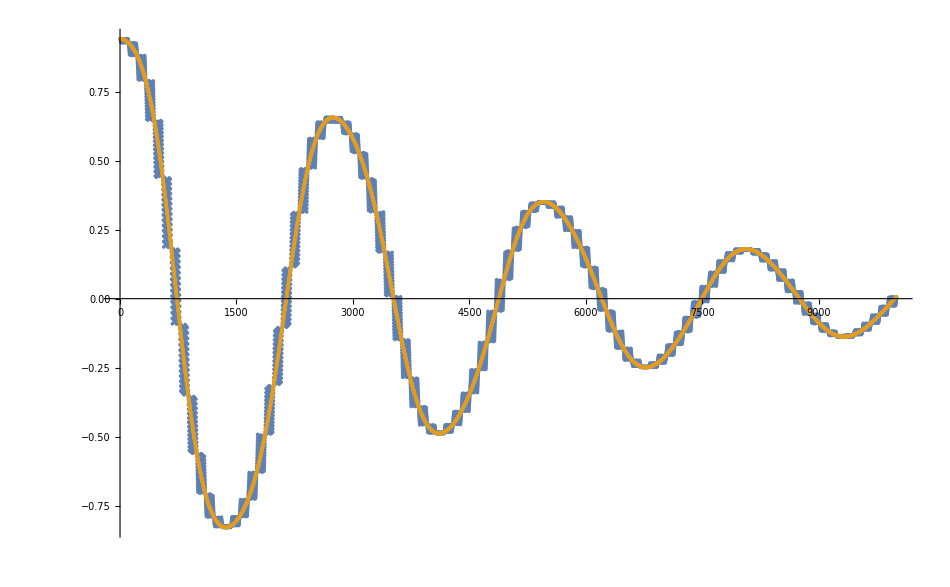

```mathematica
Ntočk=10000;
Njedrov=Length@Kernels[];
ListPlot[
	{rjivjiP[[1;;-1;;Round[(T/dt)/Ntočk],  1,  1]],rjivji[[1;;(T/dt)/Njedrov;;Round[(T/dt)/Ntočk /Njedrov],  1,  1]]},
	PlotRange->All
]
```

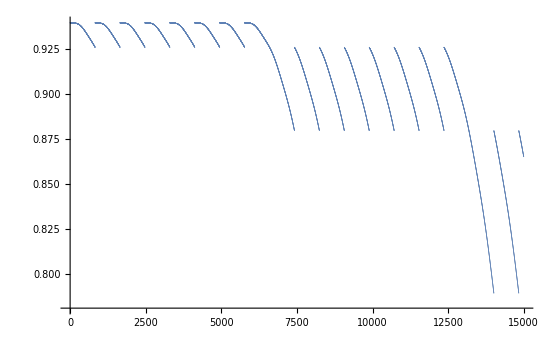

```mathematica
ListPlot[
	rjivjiP[[1;;150000;;10,  1,  1]],
	PlotRange->All,PlotStyle->Directive[PointSize->.001]
]
```

Tudi pri Do in nasploh pri veliko funkcijah se tko specificira območje. Pogosto lah kr uganemo, da se tko, ker je tko smiselno!

```mathematica
Remove@f;
MatrixForm@Table[
	f[i1,i2,i3],
2,{i1,2},{i2,1,10,2},{i3,{🐶,🐱,🐧}}]
```

((f[1,1,🐶] | f[1,1,🐱] | f[1,1,🐧]
f[1,3,🐶] | f[1,3,🐱] | f[1,3,🐧]
f[1,5,🐶] | f[1,5,🐱] | f[1,5,🐧]
f[1,7,🐶] | f[1,7,🐱] | f[1,7,🐧]
f[1,9,🐶] | f[1,9,🐱] | f[1,9,🐧]) | (f[2,1,🐶] | f[2,1,🐱] | f[2,1,🐧]
f[2,3,🐶] | f[2,3,🐱] | f[2,3,🐧]
f[2,5,🐶] | f[2,5,🐱] | f[2,5,🐧]
f[2,7,🐶] | f[2,7,🐱] | f[2,7,🐧]
f[2,9,🐶] | f[2,9,🐱] | f[2,9,🐧])
(f[1,1,🐶] | f[1,1,🐱] | f[1,1,🐧]
f[1,3,🐶] | f[1,3,🐱] | f[1,3,🐧]
f[1,5,🐶] | f[1,5,🐱] | f[1,5,🐧]
f[1,7,🐶] | f[1,7,🐱] | f[1,7,🐧]
f[1,9,🐶] | f[1,9,🐱] | f[1,9,🐧]) | (f[2,1,🐶] | f[2,1,🐱] | f[2,1,🐧]
f[2,3,🐶] | f[2,3,🐱] | f[2,3,🐧]
f[2,5,🐶] | f[2,5,🐱] | f[2,5,🐧]
f[2,7,🐶] | f[2,7,🐱] | f[2,7,🐧]
f[2,9,🐶] | f[2,9,🐱] | f[2,9,🐧]))

```mathematica
Table[If[PrimeQ@i,i,Nothing],{i,100}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

```mathematica
Reap, Sow
```

```mathematica
zbirka=Reap[
	Do[
		If[IntegerQ@√i,Sow[i,{"kvadrati","oboje"}]];
		If[PrimeQ@i,Sow[i,{"praštevila","oboje"}]];,
	{i,50}],
	_, Rule
][[2]]

"kvadrati"/.zbirka
```

{kvadrati→{1,4,9,16,25,36,49},oboje→{1,2,3,4,5,7,9,11,13,16,17,19,23,25,29,31,36,37,41,43,47,49},praštevila→{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47}}

{1,4,9,16,25,36,49}

```mathematica
Append
```

```mathematica
Remove[vec,f]

vec={};
AbsoluteTiming@Do[
	vec=Append[vec,f[i]],
{i,10000}]

vec={};
AbsoluteTiming@Do[
	vec=Append[vec,f[i]],
{i,20000}]
```

{1.16776,Nul}

{4.79148,Null}

```mathematica
Remove[vec,f]
vec=CreateDataStructure@"ImmutableVector";
AbsoluteTiming@Do[
	vec=vec["Append",f[i]],
{i,10000}]
```

{0.0207047,Null}

```mathematica
Short@Normal@vec
```

{f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10],«9980»,f[9991],f[9992],f[9993],f[9994],f[9995],f[9996],f[9997],f[9998],f[9999],f[10000]}

## ∪, ∩, /@, &/@, MAP, @@, @@@

```mathematica
{1,1}∪{1,2}∪{2,2}
Union[{1,1},{1,2},{2,2}]

{1,1}∩{1,2}∩{2,2}
Intersection[{1,1},{1,2},{2,2}]

Complement[{1,1,2,3,4},{2,4}]
```

{1,2}

{1,2}

{}

{}

{1,3}

```mathematica
Norm/@{{3,4},{5,12},{6,8}}
Map[Norm,({{{3,4}, {5,12}, {6,8}}, {{3,4}, {5,12}, {6,8}}, {{3,4}, {5,12}, {6,8}}, {{3,4}, {5,12}, {6,8}}, {{3,4}, {5,12}, {6,8}}}),{2}]
Map[Norm,({{{3,4}, {5,12}, {6,8}}, {{3,4}, {5,12}, {6,8}}, {{3,4}, {5,12}, {6,8}}, {{3,4}, {5,12}, {6,8}}, {{3,4}, {5,12}, {6,8}}}),{1,2}]
```

{5,13,10}

{{5,13,10},{5,13,10},{5,13,10},{5,13,10},{5,13,10}}

{7 √6,7 √6,7 √6,7 √6,7 √6}

```mathematica
If[IntegerQ@#,1,0]&/@{1,1.2,3,-4}
Map[If[IntegerQ@#,1,0]&,{1,1.2,3,-4}]
```

{1,0,1,1}

{1,0,1,1}

Stvari v seznamu na katerega Mapamo se po defaultu poračunajo pred Mapanjem. To lahko preprečimo tako:

Primer za štopanje

```mathematica
Map[AbsoluteTiming,{
	NIntegrate[Sin@ArcSinh@x,{x,0,1}],
	NIntegrate[Sin@Log@x,{x,0,1}]
}][[;;,1]]


Map[AbsoluteTiming@ReleaseHold@#&,Hold/@Unevaluated[{
	NIntegrate[Sin@ArcSinh@x,{x,0,1}],
	NIntegrate[Sin@Log@x,{x,0,1}]
}]][[;;,1]]
```

{1.×10^-7,0.}

{0.00235837,0.0071813}

```mathematica
Times@@{1,2,3,5}
```

30

```mathematica
Times@@@{{3,4},{5,12},{6,8}}
```

{12,60,48}

```mathematica
(2#1+#2)&@@@{{3,4},{5,12},{6,8}}
```

{10,22,20}

```mathematica
MatrixForm@Apply[Times,({{{3,4}, {5,12}, {6,8}}, {{3,4}, {5,12}, {6,8}}, {{3,4}, {5,12}, {6,8}}, {{3,4}, {5,12}, {6,8}}, {{3,4}, {5,12}, {6,8}}}),{2}]
```

(12 | 60 | 48
12 | 60 | 48
12 | 60 | 48
12 | 60 | 48
12 | 60 | 48)

# ARRAYSI

# [[]]

```mathematica
M=({{1, 2, 3, 4, 5, 6, 7, 8, 9, 10}, {11, 12, 13, 14, 15, 16, 17, 18, 19, 20}, {21, 22, 23, 24, 25, 26, 27, 28, 29, 30}, {31, 32, 33, 34, 35, 36, 37, 38, 39, 40}, {41, 42, 43, 44, 45, 46, 47, 48, 49, 50}, {51, 52, 53, 54, 55, 56, 57, 58, 59, 60}, {61, 62, 63, 64, 65, 66, 67, 68, 69, 70}, {71, 72, 73, 74, 75, 76, 77, 78, 79, 80}, {81, 82, 83, 84, 85, 86, 87, 88, 89, 90}, {91, 92, 93, 94, 95, 96, 97, 98, 99, 100}});
MatrixForm/@{
	M[[1;;8;;2,{4,1,-1}]],
	M[[1;;8;;2,{4,1,-1}]]=🎃;
	M,
	
	M[[1;;8;;2,{4,1,-1}]]={🐶,🐱,🐧,🐮};
	M,
	
	M[[1;;8;;2,{4,1,-1}]]={🐶,🐱,🐧};
	M,
	M[[1;;8;;2,{4,1,-1}]]=({{🐶, 🐱, 🐧}, {🐮, 🐷, 🦆}, {🦄, 👻, 👽}, {🐒, 🐸, 🐻}});
	M,
	
	M[[1;;8;;2,{4,1,-1}]]/=🍓;
	M
}
```

{(4 | 1 | 10
24 | 21 | 30
44 | 41 | 50
64 | 61 | 70),(🎃 | 2 | 3 | 🎃 | 5 | 6 | 7 | 8 | 9 | 🎃
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
🎃 | 22 | 23 | 🎃 | 25 | 26 | 27 | 28 | 29 | 🎃
31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40
🎃 | 42 | 43 | 🎃 | 45 | 46 | 47 | 48 | 49 | 🎃
51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60
🎃 | 62 | 63 | 🎃 | 65 | 66 | 67 | 68 | 69 | 🎃
71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80
81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90
91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100),(🐶 | 2 | 3 | 🐶 | 5 | 6 | 7 | 8 | 9 | 🐶
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
🐱 | 22 | 23 | 🐱 | 25 | 26 | 27 | 28 | 29 | 🐱
31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40
🐧 | 42 | 43 | 🐧 | 45 | 46 | 47 | 48 | 49 | 🐧
51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60
🐮 | 62 | 63 | 🐮 | 65 | 66 | 67 | 68 | 69 | 🐮
71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80
81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90
91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100),(🐱 | 2 | 3 | 🐶 | 5 | 6 | 7 | 8 | 9 | 🐧
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
🐱 | 22 | 23 | 🐶 | 25 | 26 | 27 | 28 | 29 | 🐧
31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40
🐱 | 42 | 43 | 🐶 | 45 | 46 | 47 | 48 | 49 | 🐧
51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60
🐱 | 62 | 63 | 🐶 | 65 | 66 | 67 | 68 | 69 | 🐧
71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80
81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90
91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100),(🐱 | 2 | 3 | 🐶 | 5 | 6 | 7 | 8 | 9 | 🐧
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
🐷 | 22 | 23 | 🐮 | 25 | 26 | 27 | 28 | 29 | 🦆
31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40
👻 | 42 | 43 | 🦄 | 45 | 46 | 47 | 48 | 49 | 👽
51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60
🐸 | 62 | 63 | 🐒 | 65 | 66 | 67 | 68 | 69 | 🐻
71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80
81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90
91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100),(🐱/🍓 | 2 | 3 | 🐶/🍓 | 5 | 6 | 7 | 8 | 9 | 🐧/🍓
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
🐷/🍓 | 22 | 23 | 🐮/🍓 | 25 | 26 | 27 | 28 | 29 | 🦆/🍓
31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40
👻/🍓 | 42 | 43 | 🦄/🍓 | 45 | 46 | 47 | 48 | 49 | 👽/🍓
51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60
🐸/🍓 | 62 | 63 | 🐒/🍓 | 65 | 66 | 67 | 68 | 69 | 🐻/🍓
71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80
81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90
91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100)}

# levelspecksi, Total, Acumulate, Differences

Skoraj vedno velja: Če bi bilo smiselno za nek ukaz, da ma levelspec, potem ga tut ma!. Je pa pomavadi opcijski.

Tako, kot axis v Python Numpyju

```mathematica
M=({{1, 2, 3, 4, 5, 6, 7, 8, 9, 10}, {11, 12, 13, 14, 15, 16, 17, 18, 19, 20}, {21, 22, 23, 24, 25, 26, 27, 28, 29, 30}, {31, 32, 33, 34, 35, 36, 37, 38, 39, 40}, {41, 42, 43, 44, 45, 46, 47, 48, 49, 50}, {51, 52, 53, 54, 55, 56, 57, 58, 59, 60}, {61, 62, 63, 64, 65, 66, 67, 68, 69, 70}, {71, 72, 73, 74, 75, 76, 77, 78, 79, 80}, {81, 82, 83, 84, 85, 86, 87, 88, 89, 90}, {91, 92, 93, 94, 95, 96, 97, 98, 99, 100}});

Total@M[[1]]
Total@M
Total[M,{1}]
Total[M,{2}]
Total@Total@M
Total[M,{1,2}]
Total[M,2]
```

55

{460,470,480,490,500,510,520,530,540,550}

{460,470,480,490,500,510,520,530,540,550}

{55,155,255,355,455,555,655,755,855,955}

5050

5050

5050

Total je hitrejši od vsote

```mathematica
Nmax=10^5;

Map[AbsoluteTiming@ReleaseHold@#&,Hold/@Unevaluated[{

	∑_(i=1)^Nmax i^-2,
	∑_(i=1)^Nmax i^-2.0,
	Total@(Range[Nmax]^-2.0)


}]][[;;,1]]
```

{1.73886,0.00652585,0.00213363}

Accumulate je en redkih, ki bi lah mel pa nima levelspcksa (13.1)

```mathematica
Accumulate@M[[1]]
MatrixForm/@{
	Accumulate@M,
	Accumulate/@M
}
(*@ ma prednost pred /@, drugač pa oklepaji če smo v dvomih ne škodujejo*)
```

{1,3,6,10,15,21,28,36,45,55}

{(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
12 | 14 | 16 | 18 | 20 | 22 | 24 | 26 | 28 | 30
33 | 36 | 39 | 42 | 45 | 48 | 51 | 54 | 57 | 60
64 | 68 | 72 | 76 | 80 | 84 | 88 | 92 | 96 | 100
105 | 110 | 115 | 120 | 125 | 130 | 135 | 140 | 145 | 150
156 | 162 | 168 | 174 | 180 | 186 | 192 | 198 | 204 | 210
217 | 224 | 231 | 238 | 245 | 252 | 259 | 266 | 273 | 280
288 | 296 | 304 | 312 | 320 | 328 | 336 | 344 | 352 | 360
369 | 378 | 387 | 396 | 405 | 414 | 423 | 432 | 441 | 450
460 | 470 | 480 | 490 | 500 | 510 | 520 | 530 | 540 | 550),(1 | 3 | 6 | 10 | 15 | 21 | 28 | 36 | 45 | 55
11 | 23 | 36 | 50 | 65 | 81 | 98 | 116 | 135 | 155
21 | 43 | 66 | 90 | 115 | 141 | 168 | 196 | 225 | 255
31 | 63 | 96 | 130 | 165 | 201 | 238 | 276 | 315 | 355
41 | 83 | 126 | 170 | 215 | 261 | 308 | 356 | 405 | 455
51 | 103 | 156 | 210 | 265 | 321 | 378 | 436 | 495 | 555
61 | 123 | 186 | 250 | 315 | 381 | 448 | 516 | 585 | 655
71 | 143 | 216 | 290 | 365 | 441 | 518 | 596 | 675 | 755
81 | 163 | 246 | 330 | 415 | 501 | 588 | 676 | 765 | 855
91 | 183 | 276 | 370 | 465 | 561 | 658 | 756 | 855 | 955)}

```mathematica
Differences@{a, b, c, d, e}
Differences@Differences@{a, b, c, d, e}
Differences[{a, b, c, d, e},2]
```

{-a+b,-b+c,-c+d,-d+e}

{a-2 b+c,b-2 c+d,c-2 d+e}

{a-2 b+c,b-2 c+d,c-2 d+e}

Tako lahko tudi numerično odvajamo

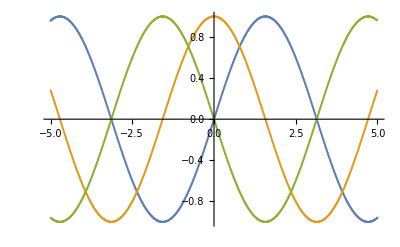

```mathematica
dx=.01; xmin=-5; xmax=5;

ran=Range[xmin,xmax,dx];
s=Sin@ran;
ListPlot[Transpose/@{
	{ran,s},
	{Range[xmin+dx/2,xmax-dx/2,dx],  (Differences@s)/dx},
	{Range[xmin+dx,xmax-dx,dx],  Differences[s,2]/dx^2}
}]
```

Za vajo probej z Accumulate definirat Integr[f[x],xmin,xmax,dx,stopnja], ki numerično integrira

# PREOBLIKOVANJE

```mathematica
arr=({{1, 2, 3, 4, 5}, {14, 15, 16, 17, 6}, {13, 20, {19,🦆,🎃}, 18, 7}, {12, 11, 10, 9, 8}});
Dimensions@arr
Length@arr
```

{4,5}

4

```mathematica
s=Range[2*3*4];
arr=ArrayReshape[s,{2,3,4}];
arr2=ArrayReshape[arr,{6,4}];

MatrixForm/@{arr,arr2}
```

{((1
2
3
4) | (5
6
7
8) | (9
10
11
12)
(13
14
15
16) | (17
18
19
20) | (21
22
23
24)),(1 | 2 | 3 | 4
5 | 6 | 7 | 8
9 | 10 | 11 | 12
13 | 14 | 15 | 16
17 | 18 | 19 | 20
21 | 22 | 23 | 24)}

```mathematica
arr=ArrayReshape[s,{2,3,4}];
(Print/@{#,""})&/@{
	arr,
	Flatten[arr,1],
	Flatten[arr,2],
	Flatten@arr
};
```

{{{1,2,3,4},{5,6,7,8},{9,10,11,12}},{{13,14,15,16},{17,18,19,20},{21,22,23,24}}}

{{1,2,3,4},{5,6,7,8},{9,10,11,12},{13,14,15,16},{17,18,19,20},{21,22,23,24}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24}

```mathematica
MatrixForm[({{👻, 👽, 🤖, 🐧, 😺, 🙉}, {🐶, 🐺, 🦆, 🦁, 🐯, 🦒}, {🦊, 🦝, 🐮, 🐷, 🐗, 🐭}})ᵀ]

Dimensions/@{
	arr,
	Transpose[arr,InversePermutation@{1,2,3}],(*permutacija osi*)
	
	arrᵀ,
	Transpose[arr,InversePermutation@{2,1,3}],(*permutacija osi*)
	
	Transpose[arr,InversePermutation@{1,3,2}] (*permutacija osi*)
}
```

(👻 | 🐶 | 🦊
👽 | 🐺 | 🦝
🤖 | 🦆 | 🐮
🐧 | 🦁 | 🐷
😺 | 🐯 | 🐗
🙉 | 🦒 | 🐭)

{{2,3,4},{2,3,4},{3,2,4},{3,2,4},{2,4,3}}

```mathematica
arr3=({{1, 2+3ⅈ}, {4, 5}, {6, 7}});
arr3†
ConjugateTranspose@arr3
```

{{1,4,6},{2-3 ⅈ,5,7}}

{{1,4,6},{2-3 ⅈ,5,7}}

```mathematica
Append[{🦆,🐶,🐺,🦁,🐯},🦒]
Prepend[{🐶,🐺,🦁,🐯,🦒},🦆]
Insert[{🦆,🐶,🦁,🐯,🦒},🐺,3]


{Splice@{🦆,🐶,🐺,🦁,🐯,🦒} }
Join[{🦆,🐶,🐺,🦁},{🐯,🦒}]
Join@@{{🦆,🐶,🐺,🦁},{🐯,🦒}}
Catenate@{{🦆,🐶,🐺,🦁},{🐯,🦒}}


s=RandomInteger[100,20]
Split[s,#1<#2&] (*razdeli v skupke, kjer za sosednja elementa v skupku velja pravilo*)
```

{🦆,🐶,🐺,🦁,🐯,🦒}

{🦆,🐶,🐺,🦁,🐯,🦒}

{🦆,🐶,🐺,🦁,🐯,🦒}

«4 more identical outputs»

{7,27,27,68,6,8,11,46,89,35,25,1,32,58,43,12,11,30,47,75}

{{7,27},{27,68},{6,8,11,46,89},{35},{25},{1,32,58},{43},{12},{11,30,47,75}}

```mathematica
arr=({{👻, 👽, 🤖, 🐧, 😺, 🙉}, {🐶, 🐺, 🦆, 🦁, 🐯, 🦒}, {🦊, 🦝, 🐮, 🐷, 🐗, 🐭}, {🐹, 🐰, 🐻, 🐌, 🐳, 🐨}, {🐼, 🐸, 🦓, 🐴, 🦄, 🐔}});
MatrixForm@Partition[arr,{2,3}]  (*Partition vam bo prav prišel pri uganki!!!!!!*)
```

((👻 | 👽 | 🤖
🐶 | 🐺 | 🦆) | (🐧 | 😺 | 🙉
🦁 | 🐯 | 🦒)
(🦊 | 🦝 | 🐮
🐹 | 🐰 | 🐻) | (🐷 | 🐗 | 🐭
🐌 | 🐳 | 🐨))

```mathematica
MatrixForm@ArrayFlatten@({{({{👻, 👽}, {🐶, 🐺}}), ({{🤖, 🐧}, {🦆, 🦁}}), ({{😺, 🙉}, {🐯, 🦒}})}, {({{🦊, 🦝}, {🐹, 🐰}, {🐼, 🐸}}), ({{🐮, 🐷}, {🐻, 🐌}, {🦓, 🐴}}), ({{🐗, 🐭}, {🐳, 🐨}, {🦄, 🐔}})}})
```

(👻 | 👽 | 🤖 | 🐧 | 😺 | 🙉
🐶 | 🐺 | 🦆 | 🦁 | 🐯 | 🦒
🦊 | 🦝 | 🐮 | 🐷 | 🐗 | 🐭
🐹 | 🐰 | 🐻 | 🐌 | 🐳 | 🐨
🐼 | 🐸 | 🦓 | 🐴 | 🦄 | 🐔)

```mathematica
MatrixForm/@{
	arr,
	RotateRight[arr,1],
	RotateRight[arr,{2,31}]
}
```

{(👻 | 👽 | 🤖 | 🐧 | 😺 | 🙉
🐶 | 🐺 | 🦆 | 🦁 | 🐯 | 🦒
🦊 | 🦝 | 🐮 | 🐷 | 🐗 | 🐭
🐹 | 🐰 | 🐻 | 🐌 | 🐳 | 🐨
🐼 | 🐸 | 🦓 | 🐴 | 🦄 | 🐔),(🐼 | 🐸 | 🦓 | 🐴 | 🦄 | 🐔
👻 | 👽 | 🤖 | 🐧 | 😺 | 🙉
🐶 | 🐺 | 🦆 | 🦁 | 🐯 | 🦒
🦊 | 🦝 | 🐮 | 🐷 | 🐗 | 🐭
🐹 | 🐰 | 🐻 | 🐌 | 🐳 | 🐨),(🐨 | 🐹 | 🐰 | 🐻 | 🐌 | 🐳
🐔 | 🐼 | 🐸 | 🦓 | 🐴 | 🦄
🙉 | 👻 | 👽 | 🤖 | 🐧 | 😺
🦒 | 🐶 | 🐺 | 🦆 | 🦁 | 🐯
🐭 | 🦊 | 🦝 | 🐮 | 🐷 | 🐗)}

V splošnem si lah predstavljamo, kot, da premikamo izhodišče na n-dim hipertorusu (ℤ_m_1×...×ℤ_m_n)

```mathematica
MatrixForm/@{
	ArrayPad[arr,2],
	ArrayPad[arr,{{0,2},{1,-1}},🍓]
}
```

{(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 👻 | 👽 | 🤖 | 🐧 | 😺 | 🙉 | 0 | 0
0 | 0 | 🐶 | 🐺 | 🦆 | 🦁 | 🐯 | 🦒 | 0 | 0
0 | 0 | 🦊 | 🦝 | 🐮 | 🐷 | 🐗 | 🐭 | 0 | 0
0 | 0 | 🐹 | 🐰 | 🐻 | 🐌 | 🐳 | 🐨 | 0 | 0
0 | 0 | 🐼 | 🐸 | 🦓 | 🐴 | 🦄 | 🐔 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(🍓 | 👻 | 👽 | 🤖 | 🐧 | 😺
🍓 | 🐶 | 🐺 | 🦆 | 🦁 | 🐯
🍓 | 🦊 | 🦝 | 🐮 | 🐷 | 🐗
🍓 | 🐹 | 🐰 | 🐻 | 🐌 | 🐳
🍓 | 🐼 | 🐸 | 🦓 | 🐴 | 🦄
🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓
🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓)}

# MATRIKE, LIN. ALGEBRA

Za praktično vse, kar se učimo pri matematiki 2 oz algebri 1, v matrični obliki  ∃ ustrezen ukaz v Mathematici. Če veste, kako se reče v angleščini, samo googlate NekiNeki Wolfram language.

## OSNOVNO

```mathematica
Norm@{3,4,12}
Normalize@{3,4,12}
```

13

{3/13,4/13,12/13}

```mathematica
{1,2,3}×{4,5,6}
{1,2,3}.{4,5,6}
({{1, 2}, {3, 4}}).({{5, 6}, {7, 8}}).{9,10}
Det@({{1, 2, 3, 4}, {12, 13, 14, 5}, {11, 16, 15, 6}, {10, 9, 8, 7}})
```

{-3,6,-3}

32

{391,887}

660

## GEOMETRIJSKO

```mathematica
Projection[{0,1,2,3,4},{5,6,7,8,9}]
```

{80/51,32/17,112/51,128/51,48/17}

```mathematica
N@ToPolarCoordinates@{-3,-1}
N@VectorAngle[{1,2,3},{4,5,6}]
```

{3.16228,-2.81984}

0.225726

```mathematica
(MatrixForm@N@#)&/@{
	RotationMatrix[12°],
	RotationMatrix[12°,{3,4,5}],  (*okoli ⇀ *)
	RotationMatrix[12,{{3,4,5,6},{7,8,9,10}}]  (* en ⇀ zavrti proti drugemu za 12*) 
}
```

{(0.978148 | -0.207912
0.207912 | 0.978148),(0.982081 | -0.141771 | 0.124168
0.15226 | 0.98514 | -0.0794685
-0.111057 | 0.0969504 | 0.989074),(0.890698 | -0.18244 | -0.255577 | -0.328715
0.0575229 | 0.953156 | -0.151211 | -0.255577
0.224348 | 0.0887521 | 0.953156 | -0.18244
0.391173 | 0.224348 | 0.0575229 | 0.890698)}

```mathematica
(MatrixForm@FullSimplify@#)&/@{
	EulerMatrix[{10°,20°,30°}, {1,1,1}],
	EulerMatrix[{10°,20°,30°}, {2,2,2}],
	EulerMatrix[{10°,20°,30°}, {3,3,3}],
	
	EulerMatrix[N@{10°,20°,30°}, {1,2,3}],
	EulerMatrix[N@{10°,20°,30°}, {3,2,3}],
	EulerMatrix[N@{10°,20°,30°}]
}
```

{(1 | 0 | 0
0 | 1/2 | -(√3)/2
0 | (√3)/2 | 1/2),(1/2 | 0 | (√3)/2
0 | 1 | 0
-(√3)/2 | 0 | 1/2),(1/2 | -(√3)/2 | 0
(√3)/2 | 1/2 | 0
0 | 0 | 1),(0.813798 | -0.469846 | 0.34202
0.543838 | 0.823173 | -0.163176
-0.204874 | 0.318796 | 0.925417),(0.71461 | -0.613092 | 0.336824
0.633718 | 0.771281 | 0.0593912
-0.296198 | 0.17101 | 0.939693),(0.71461 | -0.613092 | 0.336824
0.633718 | 0.771281 | 0.0593912
-0.296198 | 0.17101 | 0.939693)}

```mathematica
EulerAngles[({{1, 0, 0}, {0, 1/2, -(√3)/2}, {0, (√3)/2, 1/2}}),{1,2,3}]
```

{π/3,0,0}

```mathematica
(MatrixForm@FullSimplify@#)&/@{
	RollPitchYawMatrix[{10°,20°,30°}, {1,1,1}],
	
	RollPitchYawMatrix[N@{10°,20°,30°}, {1,2,3}],
	RollPitchYawMatrix[N@{10°,20°,30°}, {3,2,1}],
	RollPitchYawMatrix[N@{10°,20°,30°}]
}
```

{(1 | 0 | 0
0 | 1/2 | -(√3)/2
0 | (√3)/2 | 1/2),(0.813798 | -0.44097 | 0.378522
0.469846 | 0.882564 | 0.0180283
-0.34202 | 0.163176 | 0.925417),(0.925417 | -0.163176 | 0.34202
0.318796 | 0.823173 | -0.469846
-0.204874 | 0.543838 | 0.813798),(0.925417 | -0.163176 | 0.34202
0.318796 | 0.823173 | -0.469846
-0.204874 | 0.543838 | 0.813798)}

```mathematica
360/(2π)RollPitchYawAngles[({{0.8137976813493738, -0.44096961052988237, 0.37852230636979245}, {0.46984631039295416, 0.8825641192593856, 0.01802831123629725}, {-0.3420201433256687, 0.16317591116653482, 0.9254165783983234}}),{1,2,3}]
```

{10.,20.,30.}

```mathematica
PribližnoRM=({{0.8138, -0.44097, 0.37852}, {0.46985, 0.88256, 0.01803}, {-0.34202, 0.16318, 0.92542}});
```

```mathematica
360/(2π)RollPitchYawAngles[PribližnoRM,{1,2,3}]
```

RollPitchYawAngles::rotm: {{0.8138,-0.44097,0.37852},{0.46985,0.88256,0.01803},{-0.34202,0.16318,0.92542}} is not a 3 x 3 rotation matrix.

1/π 180 RollPitchYawAngles[{{0.8138,-0.44097,0.37852},{0.46985,0.88256,0.01803},{-0.34202,0.16318,0.92542}},{1,2,3}]

```mathematica
360/(2π)RollPitchYawAngles[  Orthogonalize@PribližnoRM,  {1,2,3}]
```

{9.99993,19.9998,29.9999}

## RVKF, in podobno

```mathematica
{M1,M2}={({{1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13}, {38, 39, 40, 41, 42, 43, 44, 45, 46, 47, 48, 49, 14}, {37, 68, 69, 70, 71, 72, 73, 74, 75, 76, 77, 50, 15}, {36, 67, 90, 91, 92, 93, 94, 95, 96, 97, 78, 51, 16}, {35, 66, 89, 104, 103, 102, 101, 100, 99, 98, 79, 52, 17}, {34, 65, 88, 87, 86, 85, 84, 83, 82, 81, 80, 53, 18}, {33, 64, 63, 62, 61, 60, 59, 58, 57, 56, 55, 54, 19}, {32, 31, 30, 29, 28, 27, 26, 25, 24, 23, 22, 21, 20}}),({{1, 2, 3, 4, 5, 6, 7}, {30, 31, 32, 33, 34, 35, 8}, {29, 52, 53, 54, 55, 36, 9}, {28, 51, 66, 67, 56, 37, 10}, {27, 50, 65, 68, 57, 38, 11}, {26, 49, 64, 69, 58, 39, 12}, {25, 48, 63, 70, 59, 40, 13}, {24, 47, 62, 61, 60, 41, 14}, {23, 46, 45, 44, 43, 42, 15}, {22, 21, 20, 19, 18, 17, 16}})};
(MatrixForm@RowReduce@#)&/@{M1,M2}

MatrixRank/@{M1,M2}
(Length@NullSpace@#)&/@{M1,M2}
(Length@#[[1]])&/@{M1,M2}

((MatrixForm@#)&/@(NullSpace@#))&/@{M1,M2}
(MatrixForm@LowerTriangularize@#)&/@{M1,M2}
(MatrixForm@UpperTriangularize@#)&/@{M1,M2}
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | -1 | -2 | -3 | -4 | -5 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)}

{8,7}

{5,0}

{13,7}

{{(0
0
0
5
-6
0
0
0
0
1
0
0
0),(0
0
0
4
-5
0
0
0
1
0
0
0
0),(0
0
0
3
-4
0
0
1
0
0
0
0
0),(0
0
0
2
-3
0
1
0
0
0
0
0
0),(0
0
0
1
-2
1
0
0
0
0
0
0
0)},{}}

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
38 | 39 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
37 | 68 | 69 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
36 | 67 | 90 | 91 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
35 | 66 | 89 | 104 | 103 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
34 | 65 | 88 | 87 | 86 | 85 | 0 | 0 | 0 | 0 | 0 | 0 | 0
33 | 64 | 63 | 62 | 61 | 60 | 59 | 0 | 0 | 0 | 0 | 0 | 0
32 | 31 | 30 | 29 | 28 | 27 | 26 | 25 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0
30 | 31 | 0 | 0 | 0 | 0 | 0
29 | 52 | 53 | 0 | 0 | 0 | 0
28 | 51 | 66 | 67 | 0 | 0 | 0
27 | 50 | 65 | 68 | 57 | 0 | 0
26 | 49 | 64 | 69 | 58 | 39 | 0
25 | 48 | 63 | 70 | 59 | 40 | 13
24 | 47 | 62 | 61 | 60 | 41 | 14
23 | 46 | 45 | 44 | 43 | 42 | 15
22 | 21 | 20 | 19 | 18 | 17 | 16)}

{(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
0 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 14
0 | 0 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 50 | 15
0 | 0 | 0 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 78 | 51 | 16
0 | 0 | 0 | 0 | 103 | 102 | 101 | 100 | 99 | 98 | 79 | 52 | 17
0 | 0 | 0 | 0 | 0 | 85 | 84 | 83 | 82 | 81 | 80 | 53 | 18
0 | 0 | 0 | 0 | 0 | 0 | 59 | 58 | 57 | 56 | 55 | 54 | 19
0 | 0 | 0 | 0 | 0 | 0 | 0 | 25 | 24 | 23 | 22 | 21 | 20),(1 | 2 | 3 | 4 | 5 | 6 | 7
0 | 31 | 32 | 33 | 34 | 35 | 8
0 | 0 | 53 | 54 | 55 | 36 | 9
0 | 0 | 0 | 67 | 56 | 37 | 10
0 | 0 | 0 | 0 | 57 | 38 | 11
0 | 0 | 0 | 0 | 0 | 39 | 12
0 | 0 | 0 | 0 | 0 | 0 | 13
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)}

Je pa treba pazit, če obravnavamo po parametru, Mathematica deli z neznanko

```mathematica
M=({{1, 0, 1-a, 0, -1}, {2, -a, 2, -1, 0}, {0, 1, -2, 1, -2}});
(MatrixForm@RowReduce@#)&/@{M,M/.a->1}
```

{(1 | 0 | 1-a | 0 | -1
0 | 1 | -2 | 0 | 0
0 | 0 | 0 | 1 | -2),(1 | 0 | 0 | 0 | -1
0 | 1 | -2 | 1 | -2
0 | 0 | 0 | 0 | 0)}

## LASTNI ⇀ in VREDNOSTI

```mathematica
M=({{1, 2, 3, 4, 5, 6, 7, 8}, {28, 29, 30, 31, 32, 33, 34, 9}, {27, 48, 49, 50, 51, 52, 35, 10}, {26, 47, 60, 61, 62, 53, 36, 11}, {25, 46, 59, 64, 63, 54, 37, 12}, {24, 45, 58, 57, 56, 55, 38, 13}, {23, 44, 43, 42, 41, 40, 39, 14}, {22, 21, 20, 19, 18, 17, 16, 15}});
MatrixForm/@(Eigenvectors@N@M)
Eigenvalues@N@M
(*Eigensystem@N@M*)
```

{(-0.0424304+0. ⅈ
-0.268288+0. ⅈ
-0.402729+0. ⅈ
-0.454965+0. ⅈ
-0.462087+0. ⅈ
-0.440797+0. ⅈ
-0.350502+0. ⅈ
-0.162357+0. ⅈ),(-0.185299+0. ⅈ
-0.402543+0. ⅈ
-0.00938961+0. ⅈ
0.350695+0. ⅈ
0.405823+0. ⅈ
0.155884+0. ⅈ
-0.474166+0. ⅈ
-0.516452+0. ⅈ),(0.254384+0. ⅈ
-0.290052+0. ⅈ
-0.195733+0. ⅈ
0.221061+0. ⅈ
0.348231+0. ⅈ
-0.0232549+0. ⅈ
-0.538655+0. ⅈ
0.593316+0. ⅈ),(0.0205946+0.381742 ⅈ
0.587134+0. ⅈ
0.073632-0.443279 ⅈ
-0.145735-0.000239332 ⅈ
-0.0383887+0.160517 ⅈ
-0.160049+0.222455 ⅈ
-0.322636-0.0905996 ⅈ
-0.0481428-0.262688 ⅈ),(0.0205946-0.381742 ⅈ
0.587134+0. ⅈ
0.073632+0.443279 ⅈ
-0.145735+0.000239332 ⅈ
-0.0383887-0.160517 ⅈ
-0.160049-0.222455 ⅈ
-0.322636+0.0905996 ⅈ
-0.0481428+0.262688 ⅈ),(-0.0239547+0. ⅈ
0.121181+0. ⅈ
-0.428183+0. ⅈ
0.27625+0. ⅈ
0.519861+0. ⅈ
-0.641352+0. ⅈ
0.204246+0. ⅈ
-0.042224+0. ⅈ),(-0.193947+0. ⅈ
0.445598+0. ⅈ
-0.728986+0. ⅈ
0.320476+0. ⅈ
-0.0276011+0. ⅈ
0.269858+0. ⅈ
-0.199613+0. ⅈ
0.127558+0. ⅈ),(0.0108972+0. ⅈ
-0.0801478+0. ⅈ
0.427365+0. ⅈ
-0.732243+0. ⅈ
0.496838+0. ⅈ
-0.160616+0. ⅈ
0.0441336+0. ⅈ
-0.00656134+0. ⅈ)}

{290.231+0. ⅈ,22.1379+0. ⅈ,10.0199+0. ⅈ,-4.45938+7.52123 ⅈ,-4.45938-7.52123 ⅈ,4.92688+0. ⅈ,-4.62244+0. ⅈ,-1.77454+0. ⅈ}

## MATRIČNE FUNKCIJE

```mathematica
M=({{1, 2, 3}, {8, 9, 4}, {7, 6, 5}});

MatrixForm/@{

	M^-1,
	Inverse@M,
	
	M^3,
	MatrixPower[M, 3],
	
	Sin@M+Cos@M,
	MatrixFunction[Sin@#+Cos@# &, 1.0 M]
	
}
```

{(1 | 1/2 | 1/3
1/8 | 1/9 | 1/4
1/7 | 1/6 | 1/5),(-7/16 | -1/6 | 19/48
1/4 | 1/3 | -5/12
5/16 | -1/6 | 7/48),(1 | 8 | 27
512 | 729 | 64
343 | 216 | 125),(524 | 574 | 396
1636 | 1785 | 1208
1364 | 1482 | 1012),(Cos[1]+Sin[1] | Cos[2]+Sin[2] | Cos[3]+Sin[3]
Cos[8]+Sin[8] | Cos[9]+Sin[9] | Cos[4]+Sin[4]
Cos[7]+Sin[7] | Cos[6]+Sin[6] | Cos[5]+Sin[5]),(-0.926026 | -0.261501 | 0.675513
0.469532 | 0.404607 | -0.660778
0.565839 | -0.233399 | 0.0665085)}

# DRUGO

# ISKANJE, BRISANJE, POD..,

## ISKANJE, BRISANJE

```mathematica
MemberQ[{🦆,🐶,🐺,🦁,🐯,🦒},🐻]
MemberQ[{🦆,🐶,🐺,🦁,🐯,🦒},🦁]
MemberQ[{🦆,🐶,🐺,{🦁},🐯,🦒},🦁]
MemberQ[{🦆,🐶,🐺,{🦁},🐯,🦒},🦁,{2}]
MemberQ[{🦆,🐶,🐺,{🦁},🐯,🦒},🐯,{2}]
MemberQ[{🦆,🐶,🐺,{🦁},🐯,🦒},🐯,2]
```

False

True

False

True

False

True

```mathematica
s={🍓,2,{3,{🍓,🍓}},4,5,🍓,7};
Position[s,🍓]
```

{{1},{3,2,1},{3,2,2},{6}}

Lahko tudi z vzorcem podamo splošno obliko, ki jo iščemo:

```mathematica
s={√(🍓^2+🫐^3),2,{3,{√(🍓^2+🍔^3),🍓}},4,5,🍓^3,7};
pos=Position[s,√(_Symbol^2+_Symbol^3)]
Delete[s,pos]
```

{{1},{3,2,1}}

{2,{3,{🍓}},4,5,🍓^3,7}

```mathematica
Cases[s,√(_Symbol^2+_Symbol^3)]
Cases[s,√(_Symbol^2+_Symbol^3),{3}]
Cases[s,√(_Symbol^2+_Symbol^3),3]
Count[s,√(_Symbol^2+_Symbol^3),3]
DeleteCases[s,√(_Symbol^2+_Symbol^3),3]
```

{√(🍓^2+🫐^3)}

{√(🍓^2+🍔^3)}

{√(🍓^2+🫐^3),√(🍓^2+🍔^3)}

2

{2,{3,{🍓}},4,5,🍓^3,7}

```mathematica
s={{👻,🐧,😺,🙉,🐗},{🐶,🦆},{🦝,🐮},{🐹,🐰,🐻,🐌,🐳},{🐴,🦄,🐔}};
Position[s,_List?(Length@#<4&)]
Select[s,Length@#<4&]
```

{{2},{3},{5}}

{{🐶,🦆},{🦝,🐮},{🐴,🦄,🐔}}

```mathematica
s2={👻,🐧,😺,🙉,🐶,🐶,🐶,🐶,🦆,🦝,🦆,🦆,🐮,🦆,🐹,🐰,🐻,🐌,🐳,🐴,🦄,🐔};
Drop[s2, 2;;-1;;2]
```

{👻,😺,🐶,🐶,🦆,🦆,🐮,🐹,🐻,🐳,🦄}

```mathematica
DeleteDuplicates@s2
DeleteAdjacentDuplicates@s2
DeleteDuplicatesBy[s,Length]
```

{👻,🐧,😺,🙉,🐶,🦆,🦝,🐮,🐹,🐰,🐻,🐌,🐳,🐴,🦄,🐔}

{👻,🐧,😺,🙉,🐶,🦆,🦝,🦆,🐮,🦆,🐹,🐰,🐻,🐌,🐳,🐴,🦄,🐔}

{{👻,🐧,😺,🙉,🐗},{🐶,🦆},{🐴,🦄,🐔}}

## POD...

```mathematica
s={🦆,👽,👽,🦄,😺,🙉};
Subsets[s,{2,4}]
```

{{🦆,👽},{🦆,👽},{🦆,🦄},{🦆,😺},{🦆,🙉},{👽,👽},{👽,🦄},{👽,😺},{👽,🙉},{👽,🦄},{👽,😺},{👽,🙉},{🦄,😺},{🦄,🙉},{😺,🙉},{🦆,👽,👽},{🦆,👽,🦄},{🦆,👽,😺},{🦆,👽,🙉},{🦆,👽,🦄},{🦆,👽,😺},{🦆,👽,🙉},{🦆,🦄,😺},{🦆,🦄,🙉},{🦆,😺,🙉},{👽,👽,🦄},{👽,👽,😺},{👽,👽,🙉},{👽,🦄,😺},{👽,🦄,🙉},{👽,😺,🙉},{👽,🦄,😺},{👽,🦄,🙉},{👽,😺,🙉},{🦄,😺,🙉},{🦆,👽,👽,🦄},{🦆,👽,👽,😺},{🦆,👽,👽,🙉},{🦆,👽,🦄,😺},{🦆,👽,🦄,🙉},{🦆,👽,😺,🙉},{🦆,👽,🦄,😺},{🦆,👽,🦄,🙉},{🦆,👽,😺,🙉},{🦆,🦄,😺,🙉},{👽,👽,🦄,😺},{👽,👽,🦄,🙉},{👽,👽,😺,🙉},{👽,🦄,😺,🙉},{👽,🦄,😺,🙉}}

```mathematica
Subsequences[s,{2,4}]
```

{{🦆,👽},{👽,👽},{👽,🦄},{🦄,😺},{😺,🙉},{🦆,👽,👽},{👽,👽,🦄},{👽,🦄,😺},{🦄,😺,🙉},{🦆,👽,👽,🦄},{👽,👽,🦄,😺},{👽,🦄,😺,🙉}}

```mathematica
Permutations@{🦆,😺,🙉}
```

{{🦆,😺,🙉},{🦆,🙉,😺},{😺,🦆,🙉},{😺,🙉,🦆},{🙉,🦆,😺},{🙉,😺,🦆}}

# NAKLJUČNO, MEŠANJE, SORTIRANJE

```mathematica
RandomReal[]
MatrixForm@RandomReal[{-2,3},{4,5}]
```

0.619369

(1.46188 | 2.37783 | 2.03898 | 2.33241 | -1.3051
2.35597 | -0.761861 | 2.30718 | -1.99351 | 0.82987
1.22069 | 2.8583 | 0.123141 | -0.215573 | -0.748851
-0.462422 | 0.604239 | 1.4943 | 2.18467 | 1.0116)

```mathematica
s={🐶,🐱,🦆,🐷,🐸,🐮,🦝,🐯,🦁};
MatrixForm@RandomChoice[s,{3,6,2}]
RandomSample[s,6]
RandomSample[s,All] (*mešanje*)
```

((🐮
🐸) | (🦁
🐶) | (🐶
🐷) | (🐱
🐶) | (🦝
🐷) | (🦁
🐱)
(🦁
🐮) | (🐯
🐯) | (🐯
🦝) | (🐸
🦝) | (🐯
🐯) | (🦆
🐷)
(🐯
🐷) | (🦆
🐷) | (🐸
🦝) | (🐮
🦆) | (🦁
🐶) | (🐷
🐷))

{🦝,🦆,🦁,🐮,🐷,🐶}

{🦁,🐸,🐯,🐷,🦆,🐱,🐮,🐶,🦝}

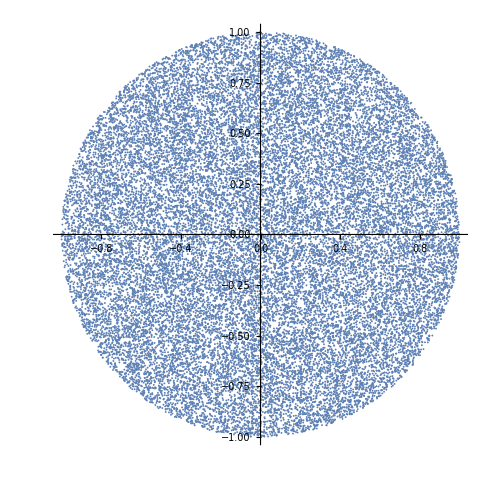

```mathematica
ListPlot[
	RandomPoint[Disk[],30000],
	AspectRatio->Automatic
]
```

```mathematica
distr=ProbabilityDistribution[ⅇ^x,{x,0,5}];
MatrixForm/@{
	RandomVariate[distr,{2,4}],
	RandomVariate[NormalDistribution[μ=1,σ=2],{3,3}]
}
```

{(0.932381 | 0.729449 | 0.831077 | 0.940266
0.0330503 | 1.01512 | 1.08646 | 0.0234305),(4.10397 | 0.719736 | -0.289589
0.312948 | 1.54728 | 1.59975
3.65606 | -1.34138 | 0.673843)}

```mathematica
SeedRandom[1234]; 
RandomPoint@Sphere[]
RandomReal[]

SeedRandom[1234];
RandomPoint@Sphere[]
RandomReal[]

RandomPoint@Sphere[]
RandomReal[]
```

{-0.303577,-0.0421634,-0.951873}

0.0116446

{-0.303577,-0.0421634,-0.951873}

0.0116446

{-0.958468,-0.27036,0.0907989}

0.759896

```mathematica
s={{👻,🐧,😺,🙉,🐗},{🐶,🦆},{🦝,🐮},{🐹,🐰,🐻,🐌,🐳},{🐴,🦄,🐔}};
SortBy[s,Length]
OrderingBy[s,Length]
```

{{🐶,🦆},{🦝,🐮},{🐴,🦄,🐔},{🐹,🐰,🐻,🐌,🐳},{👻,🐧,😺,🙉,🐗}}

{2,3,5,4,1}

```mathematica
s=Table[
	RandomInteger[{-9,9},i],
{i,RandomChoice[Range@4,15]}]
```

{{-9},{-7,8,-6},{0,6},{-2,9,4,5},{-5,8},{3},{-9},{-9,5,3},{-1,-4,9,-7},{9,6,-3,-2},{-2,-4,3},{9,0},{5,0,2,8},{-2,-3,-4},{-3,2,-7}}

```mathematica
SortBy[s,{Length,#[[1]]&}]
```

{{-9},{-9},{3},{-5,8},{0,6},{9,0},{-9,5,3},{-7,8,-6},{-3,2,-7},{-2,-4,3},{-2,-3,-4},{-2,9,4,5},{-1,-4,9,-7},{5,0,2,8},{9,6,-3,-2}}

```mathematica
{🐶,🐱,🦆,🐷}[[Ordering@{5,-8,1,2}]]
```

{🐱,🦆,🐷,🐶}

```mathematica
GatherBy[{{👻,🐧,😺,🙉,🐗},{🐶,🦆},{🦝,🐮},{🐹,🐰,🐻,🐌,🐳},{🐴,🦄,🐔}},Length]
```

{{{👻,🐧,😺,🙉,🐗},{🐹,🐰,🐻,🐌,🐳}},{{🐶,🦆},{🦝,🐮}},{{🐴,🦄,🐔}}}

```mathematica
BinLists[
	RandomReal[10,20],
{{1,2,3,5,8,13}}]
```

{{1.75413,1.68807},{2.34807,2.06316,2.42956},{3.58506},{7.87393,7.69991,6.34198,7.95595,6.06434,5.37516,6.0228,7.77424},{8.43093,9.3879,8.56579,8.66789}}

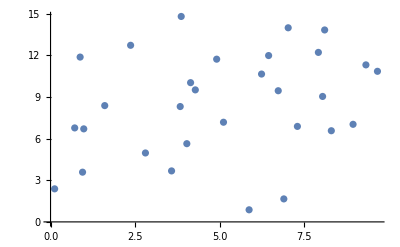

```mathematica
Nr=30;
rji={RandomReal[{0,10},Nr],RandomReal[{0,15},Nr]}ᵀ;
ListPlot@rji
```

```mathematica
MatrixForm[BL=BinLists[
	rji,
	{Range[0,10,2]},
	{{1,5,10}}
]]
```

({{0.121035,2.38065},{0.947261,3.58066}} | {{1.60337,8.37461},{0.982699,6.69961},{0.714768,6.76716}}
{{2.80741,4.96371},{3.58031,3.67182}} | {{3.83615,8.30704}}
{} | {{5.11679,7.17705},{4.28302,9.5067},{4.03195,5.63294}}
{{6.90174,1.65544}} | {{7.30337,6.87706},{6.73623,9.44515}}
{} | {{8.94971,7.02728},{8.04865,9.03387},{8.30661,6.56472}})

```mathematica
BinIndices1D[vrednosti_,meje_]:=(
	bc=BinCounts[vrednosti,{meje}];
	ord=Ordering@vrednosti;
	ord[[#[[1]];;#[[2]]]]&/@(
		Partition[
			Prepend[Accumulate@bc,0],2,1
		]+Threaded[{1,0},2]
	)
);


BinIndices[točke_,mejeje_]:=(
	točketr=točkeᵀ;
	dim=Length@točketr;
	
	
	binindjijiji=Table[
		BinIndices1D[točketr[[i]],mejeje[[i]]],
	{i,dim}];
	
	
	BloKoord=Flatten[
		CoordinateBoundsArray[{1,Length@#-1}&/@mejeje],
		dim-1
	];
	
	
	{
		BloKoord,
		
		(Intersection@@
			Table[
				binindjijiji[[i,#[[i]]]],
			{i,dim}]
		)&/@BloKoord
	}ᵀ
);





točke=Table[RandomReal[],30000,3];
mejeje=Table[Subdivide[0,1,15],3];




rez=BinIndices[točke,mejeje];
```

# DRUGO POGOSTO RAČUNANJE

## GLAJENJE

```mathematica
s={🦁,🐸,🐯,🐷,🦆,🐱,🐮,🐶,🦝};
MovingAverage[s,4]
MovingAverageCik[list_,r_]:=Mean[RotateRight[list,#]&/@Range[0,r-1]];
MovingAverageCik[s,3]
```

{1/4 (🐯+🐷+🐸+🦁),1/4 (🐯+🐷+🐸+🦆),1/4 (🐯+🐱+🐷+🦆),1/4 (🐮+🐱+🐷+🦆),1/4 (🐮+🐱+🐶+🦆),1/4 (🐮+🐱+🐶+🦝)}

{1/3 (🐶+🦁+🦝),(🐸+🦁+🦝)/3,1/3 (🐯+🐸+🦁),1/3 (🐯+🐷+🐸),1/3 (🐯+🐷+🦆),1/3 (🐱+🐷+🦆),1/3 (🐮+🐱+🦆),1/3 (🐮+🐱+🐶),1/3 (🐮+🐶+🦝)}

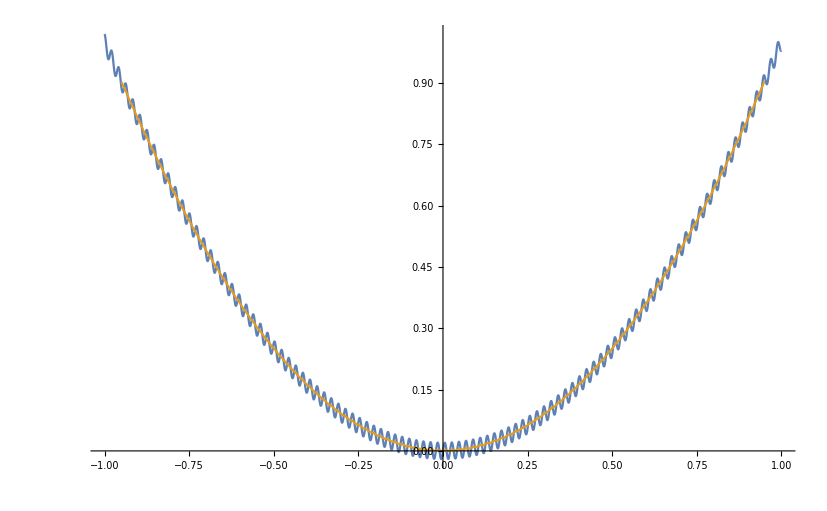

```mathematica
Ntočk=10000;
xji=Subdivide[-1.,1.,Ntočk];
yji=xji^2+.02 Sin[300 xji];
rji={xji,yji}ᵀ;

ListLinePlot@{rji,MovingAverage[rji,Round[.05 Ntočk]]}
```

```mathematica
Ntočk=10000; R=1;
φji=π Subdivide[-1.,1.,Ntočk];
zji=φji^2+.2 Sin[100 φji];
{xji,yji}=R{Cos@φji,Sin@φji};
rji3D={xji,yji,zji}ᵀ;

ListLinePlot3D[{rji3D,MovingAverageCik[rji3D,Round[.1 Ntočk]]},BoxRatios->2]
```

-Graphics3D-

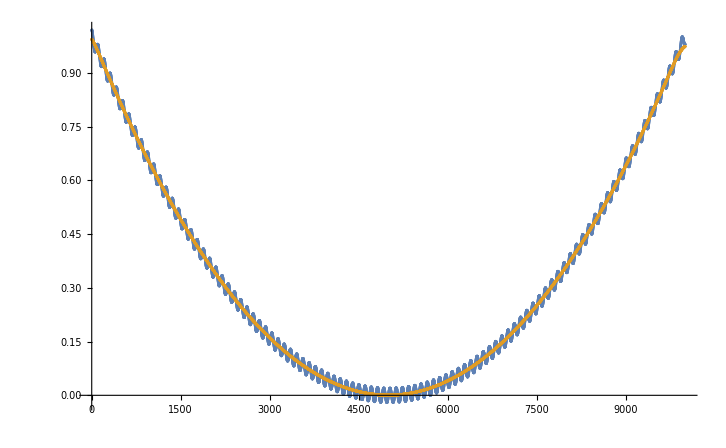

```mathematica
ListPlot@{
	rji[[;;,2]],
	LowpassFilter[rji[[;;,2]],.01]  (*ω majhen, ker gleda, kot, da so točke razmaknjene za 1*)
}
```

## FURJEJEVA VRSTA

https://www.youtube.com/watch?v=r6sGWTCMz2k&ab_channel=3Blue1Brown

https://www.youtube.com/watch?v=kvfVsu-HOTo

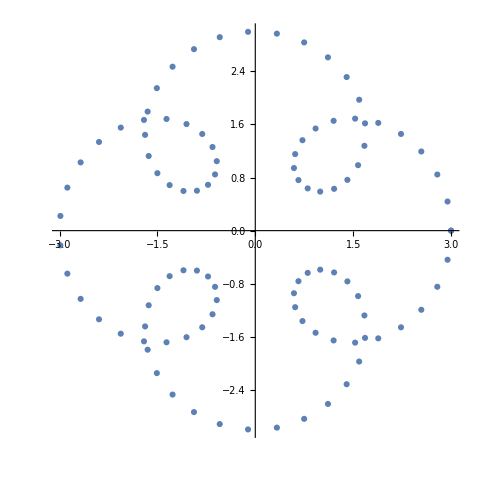

```mathematica
Remove["Global`*"];
štogl=100;

tji=Subdivide[0,N@2π,štogl-1];
rji={2Cos@tji+Cos[5tji],   2Sin@tji+Sin[5tji]}ᵀ;

ListPlot[rji,AspectRatio->Automatic]
```

```mathematica
Remove["Global`*"];
štogl=100;

tji=Subdivide[0,N@2π,štogl-1];
rji={2Cos@tji+Cos[5tji],   2Sin@tji+Sin[5tji]}ᵀ;

ListPlot[rji,AspectRatio->Automatic]





red=4;
štogl2=500;
točkeC=rji[[;;,1]]+rji[[;;,2]]ⅈ;
štogl=Length@točkeC;

cji=Mean[#]&/@(Table[ⅇ^(-1.0(n 2π ⅈ j)/štogl),{n,-red,red},{j,štogl}]*Table[točkeC,2*red+1]);(*neposortiran*)
cjisort=cji[[red+1+(Join@@Table[{-i,i},{i,0,red}])[[2;;]]    ]];
členi=(cji Table[ⅇ^(-1.0(n 2π ⅈ j)/štogl2),{n,-red,red}])[[red+1+(Join@@Table[{-i,i},{i,0,red}])[[2;;]]    ]];(*posortiran*)
konice=Table[Total@členi[[;;i]],{i,2red+1}];

konicetkart=Table[{Re[#1],Im[#1]}&/@konice,{j,štogl2}]; (*oglišče(t), red,koord*)
```

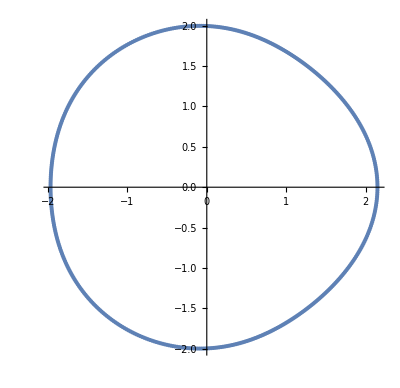

```mathematica
ListPlot[
konicetkart[[;;,-1]],
AspectRatio->Automatic]
```

## FURJEJEVA TRANSFORMACIJA

https://www.youtube.com/watch?v=spUNpyF58BY&t=3s&ab_channel=3Blue1Brown

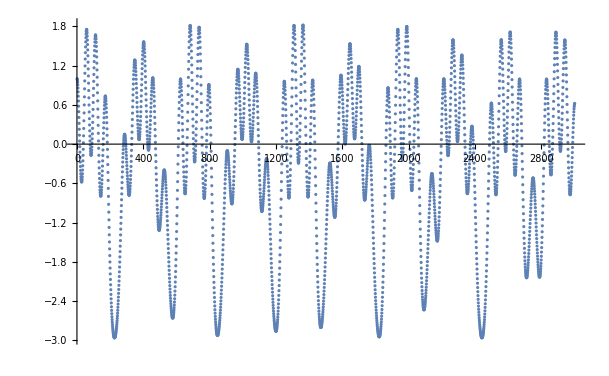

```mathematica
sol=NDSolve[
	{y''[t] == -y[t] - .2*y[t]^2 + Sin[0.2t],        y'[0]==0,        y[0]==1},
	y,{t,0,300}
];

sr = 10;(* Sample Rate*)
data = Table[Evaluate[y[t] /. sol[[1]]], {t, 0, 300, 1/sr}];
ListPlot@data
```

1/(2π)∫_(-∞)^∞ (f[t]ⅇ^(ⅈ (-1) ω t))ⅆt

```mathematica
furier[vrednosti_,sr_,ω_]:=(
	nvrednosti=Length@vrednosti;
	tjiFur=(Range@nvrednosti-1)/sr;
	Total[vrednosti ⅇ^(ⅈ ω tjiFur)]/nvrednosti
);
```

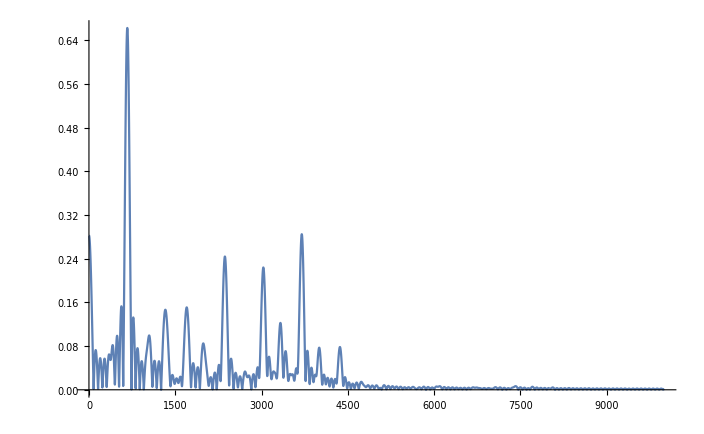

```mathematica
ListLinePlot[
	Abs@ParallelTable[furier[data,10,ω],{ω,0,3,.0003}],
	PlotRange->All
]
```

## KONVOLUCIJA

```mathematica
ListConvolve[kernel,arr]
```

Zgled za slike:

https://www.youtube.com/watch?v=8rrHTtUzyZA&ab_channel=TheJuliaProgrammingLanguage

https://www.youtube.com/watch?v=rpB6zQNsbQU&list=PLP8iPy9hna6Q2Kr16aWPOKE0dz9OnsnIJ&index=13&ab_channel=TheJuliaProgrammingLanguage

Za vajo poskusi še z ListConvolve rešiti zgled iz toplotne enačbe: ZGLED TUKI PRIDE ŠTEVILKA VIDEA!!!!

Kateri način je hitrejši?

## DRUGO

drugi filtri :   https://reference.wolfram.com/language/guide/LinearAndNonlinearFilters.html

# DRUGO

## ELIPSOIDNI, ORTOPLEKSNI ARRAY

Pride pogosteje prav, kot bi si vrjetno mislili

Za vajo ju lahko poskusite še sami definirati

```mathematica
M=DiskMatrix[{15,10}];
MatrixForm[M/.{0->🍏,1->🍓}]
```

(🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏
🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏
🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏
🍏 | 🍏 | 🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏 | 🍏 | 🍏
🍏 | 🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏 | 🍏
🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏
🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏
🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏
🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏
🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏
🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏
🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓
🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓
🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓
🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓
🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓
🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓
🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓
🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓
🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓
🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏
🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏
🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏
🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏
🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏
🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏
🍏 | 🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏 | 🍏
🍏 | 🍏 | 🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏 | 🍏 | 🍏
🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏
🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏
🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏)

```mathematica
M=DiamondMatrix[{15,13}];
MatrixForm[M/.{0->🍏,1->🍓}]
```

(🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍓 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏
🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏
🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏
🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏
🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏
🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏
🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏
🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏
🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏
🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏
🍏 | 🍏 | 🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏 | 🍏 | 🍏
🍏 | 🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏 | 🍏
🍏 | 🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏 | 🍏
🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏
🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏
🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓
🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏
🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏
🍏 | 🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏 | 🍏
🍏 | 🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏 | 🍏
🍏 | 🍏 | 🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏 | 🍏 | 🍏
🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏
🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏
🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏
🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏
🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏
🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏
🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏
🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏
🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍓 | 🍓 | 🍓 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏
🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍓 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏 | 🍏)

## CUDA LINK

GPU računanje na velikih arraysih

Zadeva ma potencial, ampak zaenkrat (Mathematica 13.1, RTX3070, 2022 novi gonilniki) še ni uporabno.  velika večina ukazov sploh ne dela, ali pa delajo zelo slabo

https://developer.nvidia.com/cuda-toolkit

https://reference.wolfram.com/language/guide/GPUComputing.html

```mathematica
Needs["CUDALink`"]
n=10000;
M=RandomReal[1,{n,n}];
AbsoluteTiming[M.M;]
MG=CUDAMemoryLoad[M];
AbsoluteTiming[A=CUDADot[MG,MG]]
B=CUDAMemoryUnload[A];
```

{11.2213,Null}

{8.88312,CUDAMemory[<32721>,Double]}